```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
evo1=Import["./Evolutions/2_3_4905_s1.mat"][[1]];
evo2=Import["./Evolutions/2_3_4905_s2.mat"][[1]];
```

```mathematica
diferences=Total[Unitize[#1-#2],2]&@@@Transpose[{evo1,evo2}]
```

{0,4372,4415,4179,3837,3672,3548,3436,3392,3362,3293,3262,3246,3222,3225,3222,3226,3224,3219,3208,3222,3214,3214,3207,3221,3201,3218,3207,3216,3205,3219,3204,3216,3208,3214,3207,3219,3202,3219,3206,3215,3205,3221,3202,3217,3209,3213,3206,3219,3204,3217,3207,3216,3204,3220,3202,3219,3207,3214,3207,3218,3203,3217,3209,3214,3205,3221,3201,3218,3207,3216,3205,3219,3204,3216,3208,3214,3207,3219,3202,3219,3206,3215,3205,3221,3202,3217,3209,3213,3206,3219,3204,3217,3207,3216,3204,3220,3202,3219,3207,3214}

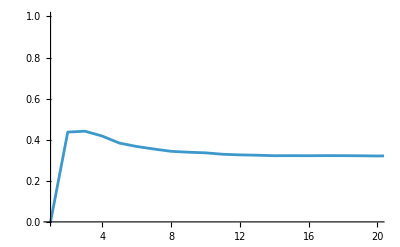

```mathematica
ListLinePlot[diferences/(100*100),PlotRange->{{1,20},{0,1}}]
```